```mathematica
(A σ^2)/2 Integrate[(1-ⅇ^-w)/w,{w,0,r^2/(2 σ^2)}]
```

ConditionalExpression[1/2 A σ^2 (EulerGamma+Gamma[0,r^2/(2 σ^2)]+Log[r^2/(2 σ^2)]), Re[r^2/σ^2]>0]

```mathematica
Integrate
```

```mathematica
u[r_]:=1/2 A σ^2 (EulerGamma+Gamma[0,r^2/(2 σ^2)]+Log[r^2/(2 σ^2)])
```

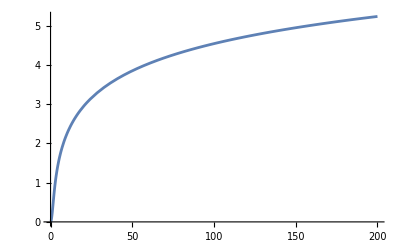

```mathematica
Plot[u[r]/.{A->1,σ->1}//Evaluate,{r,0,200}]
```

```mathematica
params={S0->1,l->1};
W=10
```

10

```mathematica
S[r_]:=S0 f[r/l]
f[x_]:=x √((0.34+0.07 x^2)/(1+0.41 x^2+0.07 x^4))
θ[ϕ_]:=ϕ/2
```

```mathematica
Q[x_,y_]:={{S[r] Cos[2θ[ϕ]],S[r] Sin[2θ[ϕ]]},{S[r] Sin[2θ[ϕ]],-S[r] Cos[2θ[ϕ]]}}/.{r->√(x^2+y^2),ϕ->ArcTan[x,y]}
```

```mathematica
tmp[x_,y_,z_]:=Block[{q},q=Eigensystem[Q[x,y]/.params];q[[1,z]]q[[2,z]]]
```

```mathematica
Eigensystem[Q[0,1]/.params]
```

{{-0.526334,0.526334},{{-0.707107,0.707107},{0.707107,0.707107}}}

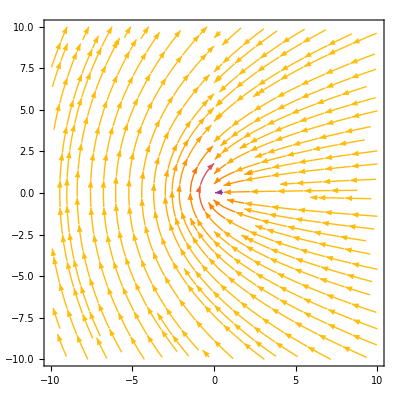

```mathematica
StreamPlot[tmp[x,y,2],{x,-W,W},{y,-W,W}]
```

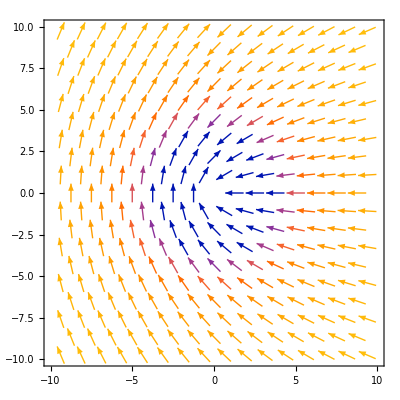

```mathematica
VectorPlot[tmp[x,y,1],{x,-W,W},{y,-W,W}];
VectorPlot[tmp[x,y,2],{x,-W,W},{y,-W,W}]
```

```mathematica
Q[-100,0]/.params//MatrixForm
```

(-0.99995 | 0
0 | 0.99995)

```mathematica
A[x_,y_]:=3IdentityMatrix[2]+Q[x,y]
Λ[x_,y_]:=3IdentityMatrix[2]+0Q[x,y]
```

```mathematica
G[x1_,y1_,x2_,y2_]=(A[x1,y1]Exp[-{x1-x2,y1-y2}.Λ[x1,y1].{x1-x2,y1-y2}/2]
+A[x2,y2]Exp[-{x1-x2,y1-y2}.Λ[x2,y2].{x1-x2,y1-y2}/2])/.params//Simplify;
```

```mathematica
G[1,2,3,4]
```

{{0.000042788,9.44999×10^-6},{9.44999×10^-6,0.0000309426}}

```mathematica
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]//Evaluate]
```

CompiledFunction[…]

```mathematica
cfG[10,2,-30,4]
```

{{0.,0.},{0.,0.}}

```mathematica
(* ===0. Initialize Parallel Kernels===*)
Print["Launching Kernels..."];
LaunchKernels[]; (*Starts worker kernels based on your CPU core count*)
DistributeDefinitions[G,cfG]; (*Sends your custom function G to all workers*)

(* ===1. Setup Grid===*)
Ngrid=64;   (*You can now likely push this to 32 or 64*)
L=40.0;
dx=L/Ngrid;
coords=Range[-L/2,L/2-dx,dx];

(*Parallel Grid Evaluation:This is where you get the biggest speedup*)
Print["Evaluating G on 4D grid in parallel..."];
GridG=ParallelTable[cfG[x1,x2,y1,y2],{x1,coords},{x2,coords},{y1,coords},{y2,coords},Method->"CoarsestGrained" (*Forces chunks of work,reducing overhead*)];

(* ===2. Forward FFT===*)
Print["Computing 4D Fourier Transforms..."];
(*Mathematica's Fourier is already multi-threaded internally via FFTW/MKL*)
G11Hat=Fourier[GridG[[All,All,All,All,1,1]]];
G12Hat=Fourier[GridG[[All,All,All,All,1,2]]];
G21Hat=Fourier[GridG[[All,All,All,All,2,1]]];
G22Hat=Fourier[GridG[[All,All,All,All,2,2]]];

freqs=N[Table[If[i<=Ngrid/2,i-1,i-1-Ngrid],{i,1,Ngrid}]*(2 Pi/L)];

(* ===3. Parallel Algebraic Equation===*)
Print["Solving algebraic equation in parallel..."];

(*We only parallelize the outermost loop (i1).Parallelizing all 4 dimensions creates massive overhead that slows Mathematica down.*)
FHat=ParallelTable[Module[{k1,k2,p1,p2,normK2,normP2,numerator},k1=freqs[[i1]];
Table[k2=freqs[[i2]];p1=freqs[[j1]];p2=freqs[[j2]];
normK2=k1^2+k2^2;
normP2=p1^2+p2^2;
If[normK2>0&&normP2>0,numerator=k1*p1*G11Hat[[i1,i2,j1,j2]]+k1*p2*G12Hat[[i1,i2,j1,j2]]+k2*p1*G21Hat[[i1,i2,j1,j2]]+k2*p2*G22Hat[[i1,i2,j1,j2]];
-numerator/(normK2*normP2),0.+0. I (*Zero DC component*)],{i2,1,Ngrid},{j1,1,Ngrid},{j2,1,Ngrid}]],{i1,1,Ngrid}];

(* ===4. Inverse FFT to Spatial Domain===*)
Print["Computing Inverse FFT..."];
fGrid=Re[InverseFourier[FHat]];

Print["Done!"];
```

Launching Kernels...

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

Evaluating G on 4D grid in parallel...

Computing 4D Fourier Transforms...

Solving algebraic equation in parallel...

Computing Inverse FFT...

Done!

```mathematica
values=Table[{coords[[i]],coords[[j]],fGrid[[i,j,i,j]]},{i,Ngrid},{j,Ngrid}];
values=Flatten[values,1];
```

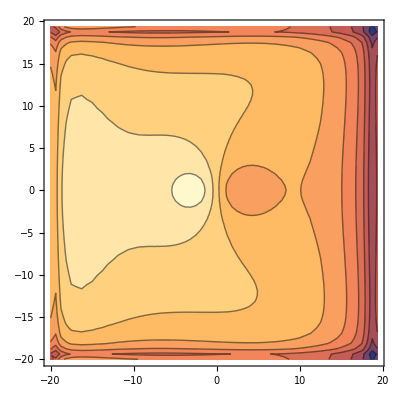

```mathematica
ListContourPlot[values,PlotRange->All]
```

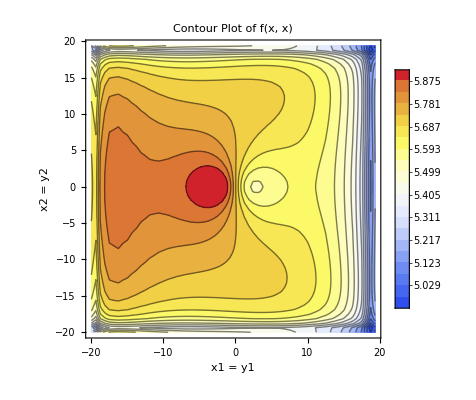

```mathematica
ListContourPlot[values,Contours->20,(*Increase this number for more contour levels/bands*)(*Maps to your actual spatial coordinates*)ColorFunction->"TemperatureMap",(*ContourStyle controls the lines themselves:*)(*Use Automatic to see the lines,or None to just see the color bands*)ContourStyle->Automatic,PlotLabel->"Contour Plot of f(x, x)",FrameLabel->{"x1 = y1","x2 = y2"},PlotLegends->Automatic]
```

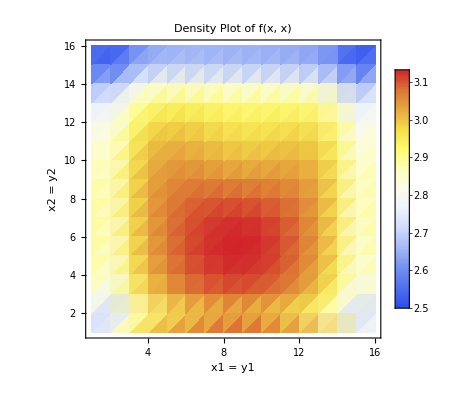

```mathematica
ListDensityPlot[fdiag,PlotLabel->"Density Plot of f(x, x)",FrameLabel->{"x1 = y1","x2 = y2"},ColorFunction->"TemperatureMap",PlotLegends->Automatic (*Adds a color bar scale on the side*)]
```